```mathematica
y={-1.48,-1.40, -1.16,-1.08,-1.02,0.14,0.51,0.53,0.078};
```

```mathematica
α=1;
σ1=0.1^2;
θ2=0;
σ2=1;
P["x|θ",{x_,θ1_}]:=PDF[NormalDistribution[θ1,σ1]][x]
P["θ",{θ_}]:=PDF[NormalDistribution[θ2,σ2]][θ]
P["θ|x",{θ_,x_}]:=Evaluate[(P["x|θ",{x,θ}]P["θ",{θ}])/(∫_(-∞)^(+∞) P["x|θ",{x,s}]P["θ",{s}]ⅆs)]
r[x_] := α Evaluate[∫_(-∞)^(+∞) P["x|θ",{x,θ}]P["θ",{θ}]ⅆθ]
ParamUpdate[x_]:=(σ/.Solve[P["θ|x",{x,x}]==PDF[NormalDistribution[x,σ]][x],{σ}])[[1]]
```

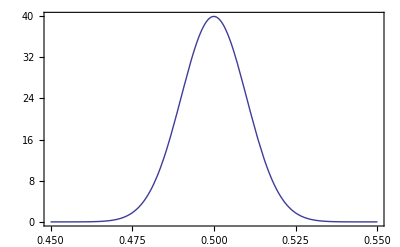

```mathematica
Plot[P["θ|x",{θ,0.5}],{θ,0.45,0.55},PlotRange->All,Frame->True]
```

```mathematica
Sample[x_,θ_,i_]:=Module[{mT,θn,q,b,μ,σ},
θn=Delete[θ,i];
mT=Length[θn];
q=Plus@@Table[P["x|θ",{x[[i]],θn[[j]]}],{j,1,mT}];
b=1/(q+r[x[[i]]]);
μ=x[[i]];
σ=ParamUpdate[μ];
If[Random[]<b q,θ[[RandomInteger[{1,mT}]]],
RandomVariate[NormalDistribution[μ,σ],1][[1]]]]
```

```mathematica
GibbsSampler[x_,n_,m_]:=Module[{N,θ,r},
N=Length[x];
θ=Table[Random[],{N}];
Do[Do[θ[[i]]=Sample[x,θ,i],{i,1,N}],{m}];
r=Table[0,{n},{N}];r[[1]]=θ;
Do[Do[θ[[i]]=Sample[x,θ,i],{i,1,N}];r[[k+1]]=(k r[[k]]+θ)/(k+1),{k,1,n-1}];
r]
```

```mathematica
GibbsSampler[y,10]
```

{{-1.47108,-1.39817,-1.15732,-1.09555,-1.01878,0.141656,0.509197,-1.47108,0.0651911},{-1.24493,-1.40408,-1.15744,-1.08234,-1.08817,0.136236,0.510678,-1.44054,0.0797601},{-1.32294,-1.40605,-1.15747,-1.0827,-1.06518,0.139739,0.510527,-1.34621,0.0829584},{-1.36594,-1.4057,-1.12291,-1.07799,-1.06485,0.140233,0.509082,-0.881135,0.0817477},{-1.38954,-1.40348,-1.12977,-1.07516,-1.05875,0.139732,0.110472,-0.6006,0.0817154},{-1.33034,-1.40113,-1.13624,-1.07831,-0.859338,-0.0783186,0.115014,-0.412228,0.0808667},{-1.35104,-1.4018,-1.13021,-0.848603,-0.881904,-0.234069,-0.0577089,-0.509631,0.0795465},{-1.36793,-1.40142,-0.922731,-0.879284,-0.898116,-0.185956,-0.187251,-0.582683,0.0796943},{-1.38004,-1.40129,-0.946613,-0.903146,-0.912032,-0.150564,-0.111111,-0.460376,0.0795992},{-1.38815,-1.40197,-0.967888,-0.922571,-0.924189,-0.123498,-0.20974,-0.361594,0.078387}}

```mathematica
data=GibbsSampler[y,1000,100];
```

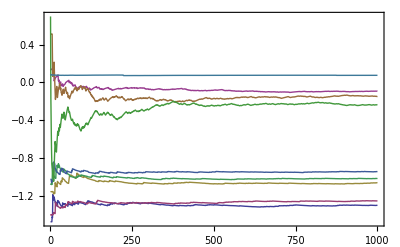

```mathematica
ListPlot[Transpose[data],Frame->True,Joined->True]
```

```mathematica
data=GibbsSampler[y,1000,1000];
```

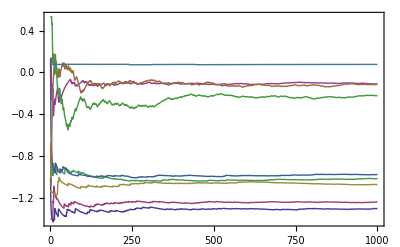

```mathematica
ListPlot[Transpose[data],Frame->True,Joined->True]
```